## Reading Packages

### Pacakges

```mathematica
Needs["Murta`"]
Needs["Marche`"]
Needs["MAFormat`"]
ip="192.168.0.13";
SetDirectory@mrtFileDirectory[];
SetSystemOptions["DataOptions"->"ReturnQuantities"->False];
```

### Auxiliar Functions

```mathematica
$titleStyle={Darker@Gray,Bold,FontFamily->"Helvetic"};
```

```mathematica
ClearAll@moveYear
moveYear[{year_,month_},steeps_Integer:12]:=DatePlus[{year,month},{steeps,"Month"}]⟦;;2⟧
moveYear[steeps_Integer:0]:=moveYear[{#⟦1⟧,#⟦2⟧},steeps]&
moveYear[0]:=Identity

(*moveYear[1][{2015,1}]*)
```

```mathematica
ClearAll@lagCompare
lagCompare[data_Symbol,keyField_String, compareField_String:"Ticket",steeps_Integer:12]:=Module[{r},
	r←data;
	(*Agreganting *)
	If[r["Data"]=={},Return@$Failed];
	r←mrtDataObject[
		 mrtVlookup[r["Data"],MapAt[moveYear[steeps],r["Data"],{All,1}]]
		,Join[r["Heads"],Rest[#<>"L"&/@r["Heads"]]]
	];
	r←mrtDataObject[
		{#⟦r.keyField⟧,If[#⟦r.compareField<>"L"⟧===Null,Null,#⟦r.compareField⟧/#⟦r.compareField<>"L"⟧-1]}&/@r⟦All⟧
		,{keyField,compareField}
	];
	r

]

(*lagCompare[r,"AnoMes","Valor",12]["Data"]*)
```

```mathematica
maGetDep[]:=Module[{sql,r,conn=marcheConn["192.168.0.13"],rule,noProd,title,grid,fileName},

	sql= "
		SELECT 
			   COD_DEPARTAMENTO as [Qtd Secoes]
			  ,rtrim([NO_DEPARTAMENTO] + '|'+ convert(char,[COD_DEPARTAMENTO])) as Departamento

		  FROM [BI].[dbo].[BI_CAD_HIERARQUIA_PRODUTO]
		  WHERE 1=1
		  and COD_DEPARTAMENTO NOT IN (99,18,17,15)
		  and no_secao not like '%zzz%'
		  GROUP BY  [NO_DEPARTAMENTO]
				   ,[COD_DEPARTAMENTO]
		  order by Departamento
	";

	r=SQLExecute[conn,sql];
	CloseSQLConnection[conn];
	<|Rule@@@r|>
]
```

## Get Data Functions

### Get Data Venda Loja

```mathematica
getVendaLoja[codLoja_List,{dtIni_,dtFim_}]:=Module[{sql,r,conn=marcheConn[ip],tab},

	sql="
		SELECT Max(data) as AnoMes
			  ,Sum(QTDE_CUPOM) as Ticket
			  ,Sum(VALOR_TOTAL) as Valor
			  ,isnull(Sum(VALOR_TOTAL)/nullif(Sum(QTDE_CUPOM),0),0) as TM
		FROM [BI].[dbo].[BI_VENDA_CUPOM]
		where 1=1
		and DATA between CONVERT(date,`1`) and CONVERT(date,`2`)
		"<>mrtSQLIn["and cod_loja in",codLoja/. {0}->{}]<>"
		group by datePart(year,[DATA]), datePart(month,[DATA])
		order by AnoMes

	";
	r←mrtSQLDataObject[conn,sql,{SQLDateTime@dtIni,SQLDateTime@dtFim,codLoja}];
	r["Data"]⟦All,r."AnoMes"⟧=#⟦1,1;;2⟧&/@r["Data"]⟦All,r."AnoMes"⟧;
	r["Data"]=Select[r,#⟦"Ticket"⟧>1000&];
	r["DtIni"]=dtIni;
	r["DtFim"]=dtFim;
	r["DtRange"]={dtIni,dtFim};
	r["CodLoja"]=codLoja;
	r["NoLoja"]=codLoja/.$lojas;
	r["Eventos"]=Flatten@Lookup[$eventosLoja,codLoja,{}];
	r
]
r←getVendaLoja[{},{{2012,1,1},{2014,8,31}}]
r["Data"]//Length

(*r←getVendaLoja[{18},{{2012,6,1},{2014,8,31}}]*)
(*r["Eventos"]*)
```

32

### Get Data Venda Departamento

```mathematica
getVendaDep[codDep_List,codLoja_List,{dtIni_,dtFim_}]:=Module[{sql,r,conn=marcheConn[ip],tab},

	sql="

		SELECT Max(data) as AnoMes
			  ,Sum([QTD_VENDA]) as Ticket --**QTDPROD
			  ,Sum([VLR_VENDA]) as Valor
			  ,isnull(Sum([VLR_VENDA])/nullif(Sum([QTD_VENDA]),0),0) as TM
		FROM [BI].[dbo].[BI_VENDA_GRUPO]
		where 1=1
		and DATA between CONVERT(date,`1`) and CONVERT(date,`2`)
		"<>mrtSQLIn["and cod_departamento in",codDep/. {0}->{}]<>"
		"<>mrtSQLIn["and cod_loja in",codLoja/. {0}->{}]<>"
		group by datePart(year,[DATA]), datePart(month,[DATA])
		order by AnoMes
	";
	
	r←mrtSQLDataObject[conn,sql,{SQLDateTime@dtIni,SQLDateTime@dtFim,codDep}];
	r["Data"]⟦All,r."AnoMes"⟧=FromDigits/@Query[;;2]@StringSplit[#,"-"]&/@r["Data"]⟦All,r."AnoMes"⟧;
	r["Data"]=Select[r,#⟦"Ticket"⟧>1000&];
	r["DtIni"]=dtIni;
	r["DtFim"]=dtFim;
	r["DtRange"]={dtIni,dtFim};
	r["CodDep"]=codDep;
	r["NoLoja"]=codDep/.$dep;
	r["Eventos"]=If[  Length@codLoja==1
					,Flatten@Lookup[$eventosLoja,First@codLoja,{}]
					,{}
				];
	r
]
r←getVendaDep[{1},{},{{2012,1,1},{2014,8,31}}];
(*r["Data"]*)
r["Data"]//Length
```

32

### Get Data Venda Departamento 2

```mathematica
getVendaDep2[codDep_List,codLoja_List,{dtIni_,dtFim_}]:=Module[{sql,r,conn=marcheConn[ip],tab},

	sql="
              SELECT Max(data) as AnoMes
                    ,Sum([QTD_CUPOM]) as Ticket
	                ,Sum([VLR_VENDA]) as Valor
					,isnull(Sum([VLR_VENDA])/nullif(Sum([QTD_CUPOM]),0),0) as TM
                 FROM [BI].[dbo].[BI_VENDA_DEPARTAMENTO]		
                 where 1=1
				and DATA between CONVERT(date,`1`) and CONVERT(date,`2`)
				"<>mrtSQLIn["and cod_departamento in",codDep/. {0}->{}]<>"
				"<>mrtSQLIn["and cod_loja in",codLoja/. {0}->{}]<>"
				group by datePart(year,[DATA]), datePart(month,[DATA])
				order by AnoMes
	";
	
	r←mrtSQLDataObject[conn,sql,{SQLDateTime@dtIni,SQLDateTime@dtFim,codDep}];
	r["Data"]⟦All,r."AnoMes"⟧=FromDigits/@Query[;;2]@StringSplit[#,"-"]&/@r["Data"]⟦All,r."AnoMes"⟧;
	r["Data"]=Select[r,#⟦"Ticket"⟧>1000&];
	r["DtIni"]=dtIni;
	r["DtFim"]=dtFim;
	r["DtRange"]={dtIni,dtFim};
	r["CodDep"]=codDep;
	r["NoLoja"]=codDep/.$dep;
	r["Eventos"]=If[  Length@codLoja==1
					,Flatten@Lookup[$eventosLoja,First@codLoja,{}]
					,{}
				];
	r
]
r←getVendaDep2[{1},{},{{2012,1,1},{2014,8,31}}];
r["Data"]//Length
```

27

```mathematica
r[0]
```

DataObject(Dimensions:{27,4})[0]

## Loading Data

### Definitions

```mathematica
$dep=maGetDep[];
$dep = Prepend[$dep, 0-> "TODOS"];
```

```mathematica
(*Eventos*)
$eventosLoja=<|
	 18->{<|"data"-> {2014,5,24},"tipo"-> "Dia%"|>}
	,12->{<|"data"-> {2014,6,26},"tipo"-> "Dia%"|>}
	, 2->{<|"data"-> {2014,2,28},"tipo"-> "Estaci"|>}
	, 7->{<|"data"-> {2014,8,9},"tipo"-> "Obra"|>}
	,12->{<|"data"-> {2013,7,4},"tipo"-> "Horti"|>}
|>;
```

```mathematica
(*Eventos*)
$eventosGlobal={
	 <|"data"-> {2012,4,8},"tipo"-> "P"|>
	,<|"data"-> {2013,3,31},"tipo"-> "P"|>
	,<|"data"-> {2014,4,20},"tipo"-> "P"|>
};
```

```mathematica
(*$infoLojas=1*)(*Select[x,Abs@DateDifference[#⟦"DtaAbertura"⟧]≤ 365&]⟦All,2⟧*)
$lojas=KeyDrop[8]@marcheGetDeParaLojas[];
$lojas = Prepend[$lojas,0-> "Grupo"];

$lojasInfo=KeyDrop[8]@marcheInfoLoja[];

$lojasMa14=Keys@Select[$lojasInfo,Abs@DateDifference[#⟦"DtaAbertura"⟧]>14×31&];
$lojasMe14=Keys@Select[$lojasInfo,Abs@DateDifference[#⟦"DtaAbertura"⟧]≤14×31&];
```

### Loading

```mathematica
$dataDepMa14=AssociationMap[(PrintTemporary@#;getVendaDep[{#},$lojasMa14,{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@KeyDrop[$dep, 0]];
$dataDepMe14=AssociationMap[(PrintTemporary@#;getVendaDep[{#},$lojasMe14,{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@KeyDrop[$dep, 0]];
```

```mathematica
$dataLoja=AssociationMap[(PrintTemporary@#;getVendaLoja[{#},{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@$lojas];
```

```mathematica
$dataLojasMa14=getVendaLoja[$lojasMa14,{{2012,1,1},{2014,8,31}}];
$dataLojasMe14=getVendaLoja[$lojasMe14,{{2012,1,1},{2014,8,31}}];
```

```mathematica
$dataDep2Ma14=AssociationMap[(PrintTemporary@#;getVendaDep2[{#},$lojasMa14,{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@$dep];
$dataDep2Me14=AssociationMap[(PrintTemporary@#;getVendaDep2[{#},$dataDepMe14,{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@$dep];
```

```mathematica
$dataDep2=AssociationMap[(PrintTemporary@#;getVendaDep2[{#},{},{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@$dep];
```

```mathematica
$dataLoja[0]
```

DataObject(Dimensions:{32,4})

```mathematica
$dataDep2[0]
```

DataObject(Dimensions:{27,4})

## Report Parts

### Plot Absolute Values

```mathematica
ClearAll@plotLagAbs
plotLagAbs[data_Symbol,field_String]:=Module[{r,ts,ts12,downTicks},

	r←data;
	ts=TimeSeries[r["Data"]⟦All,r@{"AnoMes",field}⟧];
	ts12=TimeSeriesShift[ts,{12,"Month"}];
	downTicks={DatePlus[#,15],DateString[#,{"MonthNameShort"}]}&/@DateRange[r["DtIni"],r["DtFim"],"Month"];
	DateListPlot[TimeSeriesShift[#,{15,"Day"}]&/@{ts,ts12}
		,AspectRatio->0.1
		,Joined->{True,True}
		,PlotRange->{r["DtRange"],All}
		,ImageSize->700
		,PlotStyle->{Directive[Darker@Green],Directive[LightGray]}
		,PlotLabel->Style[Row[{r["NoLoja"]," - ",field}],Gray,Bold]
		,Filling->{1->{2}}
		,GridLines->{Join[{{r["Eventos"],Directive[Red,Thick]}},{#,LightGray}&/@DateRange[r["DtIni"],r["DtFim"],"Month"]],None}
		,ImagePadding->{{50,10},{20,Automatic}}
		,FrameTicks-> {{Automatic,Automatic},{downTicks,Automatic}}
	]
]

(*plotLagAbs[r,"Valor"]*)
```

### Plot Comparativo 12m

```mathematica
ClearAll@colorLag12
colorLag12["Ticket"]=Which[
			 #1<0, Red
			,#1<5, Orange
			,#1<10,Darker@Darker@Green
			,True, Darker@Blue
]&;

colorLag12[_]=Which[
			 #1<7, Red
			,#1<10, Orange
			,#1<15,Darker@Darker@Green
			,True, Darker@Blue
]&;
```

```mathematica
Options[plotLag12Perc]={"StartDate"-> Automatic};

plotLag12Perc[data_Symbol,field_String,opts:OptionsPattern[{plotLag12Perc}]]:=Module[{r,ts,startDate,label,growthMedian,ticksDown,ticksUp(*,eventos*),eventoName},
	startDate=OptionValue["StartDate"]/.Automatic->r["DtIni"];
	r←data;
	ts=TimeSeriesShift[#,{15,"Day"}]&@lagCompare[r,"AnoMes",field,12]["Data"];
	growthMedian=mrtPerc[Median@DeleteCases[Null]@ts⟦All,2⟧,1];
	label=Style[Row[{r["NoLoja"]," - Δ%",field,"-YoY (med:",growthMedian,")"}],Gray,Bold];

	ticksUp= {#1,Style[mrtPerc[#2,1],colorLag12[field][100#2],7,Bold]}&@@@DeleteCases[ts,{_,Null}];
	ticksDown={DatePlus[#,15],Style[DateString[#,{"MonthNameShort"}],If[Mod[#⟦1⟧,2]==0,Directive[Bold,Darker@Darker@Green],Plain]]}&/@DateRange[r["DtIni"],r["DtFim"],"Month"];

	eventos=Join[
				 {#data,Directive[Blue,Thick]}&/@$eventosGlobal
				,Quiet@Check[{#,Directive[Red,Thick]}&/@r["Eventos"]⟦All,"data"⟧,{}]
				,{#,LightGray}&/@DateRange[r["DtIni"],r["DtFim"],"Month"]
				];	
	eventoName=Quiet@Check[
		Text[
				 Style[#2,Darker@Gray]
				,Scaled[{0,0.3},{#1,0}]
			]&@@@Join[Values@r["Eventos"],Values@$eventosGlobal]
	,Null];

	DateListPlot[MapAt[100#&,ts,{All,2}]
		,AspectRatio->0.15
		,Joined->{True,True}
		,PlotRange->{{startDate,r["DtFim"]},All}
		,ImageSize->500
		,PlotStyle->{Directive[Darker@Green]}
		,PlotLabel->label
		,GridLines->{eventos,{0}}
		,ImagePadding->{{50,10},{15,12}}
		,ColorFunction->(colorLag12[field][#2]&)
		,ColorFunctionScaling->False
		,Epilog->{eventoName}
		,FrameTicks-> {{Automatic,Automatic},{ticksDown,ticksUp}}

		(*,FrameTicks-> {{mrtPercentTicks,Automatic},{Automatic,Automatic}}*)
	]
]

(*Grid[{plotLag12Perc[$dataLoja[#],"Valor","StartDate"-> {2013,1,1}]}&/@{18,7,12}]*)
(*Grid[{plotLag12Perc[$dataLoja[#],"Ticket","StartDate"-> {2013,1,1}]}&/@{1,2}]*)
(*Grid[{plotLag12Perc[$dataLoja[#],"Ticket","StartDate"-> {2013,1,1}]}&/@{0}]*)
(*Grid[{plotLag12Perc[$dataDepMa14[#],"Valor","StartDate"-> {2013,1,1}]}&/@{5,2,19}]*)
(*Grid[{plotLag12Perc[$dataDepMa14[#],"Valor","StartDate"-> {2013,1,1}]}&/@{5}]*)
(*Grid[{plotLag12Perc[$dataDepMa14[#],"Ticket","StartDate"-> {2013,1,1}]}&/@{5}]*)
```

```mathematica
plotReport[data_Symbol,field_String]:=Module[{g},
	g=Grid[{{plotLag12Perc[data,field]},{plotLagAbs[data,field]}}
			,Frame-> True
			,FrameStyle->LightGray
		];
	g
]

(*plotReport[r,"Valor"]
plotReport[r,"Ticket"]
plotReport[r,"TM"]*)
```

### Plot Comparativo 01m

```mathematica
colorLag01=Which[
			 #1<0, Red
			,#1<2, Orange
			,#1<4,Darker@Darker@Green
			,True, Darker@Blue
]&;
```

```mathematica
Options[plotLag01Perc]={"StartDate"-> Automatic};

plotLag01Perc[data_Symbol,field_String,opts:OptionsPattern[{plotLag01Perc}]]:=Module[{r,ts,startDate,label,growthMedian,ticksDown,ticksUp,eventos,eventoName},
	startDate=OptionValue["StartDate"]/.Automatic->r["DtIni"];
	r←data;
	ts=TimeSeriesShift[#,{15,"Day"}]&@lagCompare[r,"AnoMes",field,01]["Data"];

	growthMedian=mrtPerc[Median@DeleteCases[Null]@ts⟦All,2⟧,1];
	label=Style[Row[{r["NoLoja"]," - Δ%",field,"-MoM (med:",growthMedian,")"}],Gray,Bold];

	ticksUp= {#1,Style[mrtPerc[#2,1],colorLag01[100#2],7,Bold]}&@@@DeleteCases[ts,{_,Null}];
	ticksDown={DatePlus[#,15],DateString[#,{"MonthNameShort"}]}&/@DateRange[r["DtIni"],r["DtFim"],"Month"];

	eventos=Join[{#data,Directive[Blue,Thick]}&/@$eventosGlobal,Quiet@Check[{#,Directive[Red,Thick]}&/@r["Eventos"]⟦All,"data"⟧,{}],{#,LightGray}&/@DateRange[r["DtIni"],r["DtFim"],"Month"]];	
	eventoName=Quiet@Check[
		Text[
				 Style[#2,Darker@Gray]
				,Scaled[{0,0.3},{#1,0}]
			]&@@@Join[Values@r["Eventos"],Values@$eventosGlobal]
	,Null];

	DateListPlot[MapAt[100#&,ts,{All,2}]
		,AspectRatio->0.15
		,Joined->{True,True}
		,PlotRange->{{startDate,r["DtFim"]},All}
		,ImageSize->500
		,PlotStyle->{Directive[Darker@Green]}
		,PlotLabel->label
		,GridLines->{eventos,{0}}
		,ImagePadding->{{50,10},{15,12}}
		,ColorFunction->(colorLag01[#2]&)
		,ColorFunctionScaling->False
		,FrameTicks-> {{Automatic,Automatic},{ticksDown,ticksUp}}
		,Epilog->{eventoName}
		(*,FrameTicks-> {{mrtPercentTicks,Automatic},{Automatic,Automatic}}*)
	]
]

(*Grid[{plotLag01Perc[$dataLoja[#],"Valor","StartDate"-> {2013,1,1}]}&/@{2,12,18,1}]*)
(*Grid[{plotLag01Perc[$dataDepMe14[#],"Valor","StartDate"-> {2013,1,1}]}&/@{5,2,19}]*)
```

```mathematica
(*plotReport[data_Symbol,field_String]:=Module[{g},
	g=Grid[{{plotLag01Perc[data,field]},{plotLagAbs[data,field]}}
			,Frame-> True
			,FrameStyle->LightGray
		];
	g
]

(*plotReport[r,"Valor"]
plotReport[r,"Ticket"]
plotReport[r,"TM"]*)*)
```

## Reports

### Loja

```mathematica
ClearAll@reportLoja;
reportLoja[field:("Valor"|"Ticket"|"TM")]:=Module[{rMe14,rMa14,rGrupo,rGrupoMe14,rGrupoMa14,plotsMe14,plotsMa14,plotGrupoMe14,plotGrupoMa14,plotGrupo,title},
	
	plotsMa14=plotLag12Perc[$dataLoja[#],field,"StartDate"-> {2013,1,1}]&/@$lojasMa14;
	plotsMe14=plotLag01Perc[$dataLoja[#],field,"StartDate"-> {2013,1,1}]&/@$lojasMe14;
	plotGrupo=plotLag12Perc[$dataLoja[0],field,"StartDate"-> {2013,1,1}];
	plotGrupoMa14=plotLag12Perc[$dataLojasMa14,field,"StartDate"-> {2013,1,1}];
	plotGrupoMe14=plotLag01Perc[$dataLojasMe14,field,"StartDate"-> {2013,1,1}];

	rMe14=maReportFrame[
		Style["MoM Lojas -14 meses\n",$titleStyle]
		,Grid[Partition[plotsMe14,2,2,1,Null],Spacings->0]
	];

	rMa14=maReportFrame[
		Style["YoY Lojas +14 meses\n",$titleStyle]
		,Grid[Partition[plotsMa14,2,2,1,Null],Spacings->0]
	];
	
	rGrupo=maReportFrame[
		Style["Grupo\n",$titleStyle],plotGrupo
	];
	
	rGrupoMa14=maReportFrame[
		Style["Grupo +14 meses\n",$titleStyle],plotGrupoMa14
	];
	
	rGrupoMe14=maReportFrame[
		Style["Grupo -14 meses\n",$titleStyle],plotGrupoMe14
	];
	
	title=Style["\nVisão Crescimento "<>field<>"\n",15,$titleStyle];

	maReportFrame[title
				,Grid[{
					{rGrupo, SpanFromLeft}
				   ,{rGrupoMa14,rGrupoMe14}
				   ,{rMa14,SpanFromLeft}
				   ,{rMe14,SpanFromLeft}
				     }]]
	

	(*maReportFrame[Style["\nVisão Crescimento "<>field<>"\n",15,$titleStyle],Grid[{{rMa14},{},{rMe14}}]]*)

] 

(*reportLoja["Valor"]*)
(*reportLoja["Ticket"]*)
(*reportLoja["TM"]*)
```

### Departamento

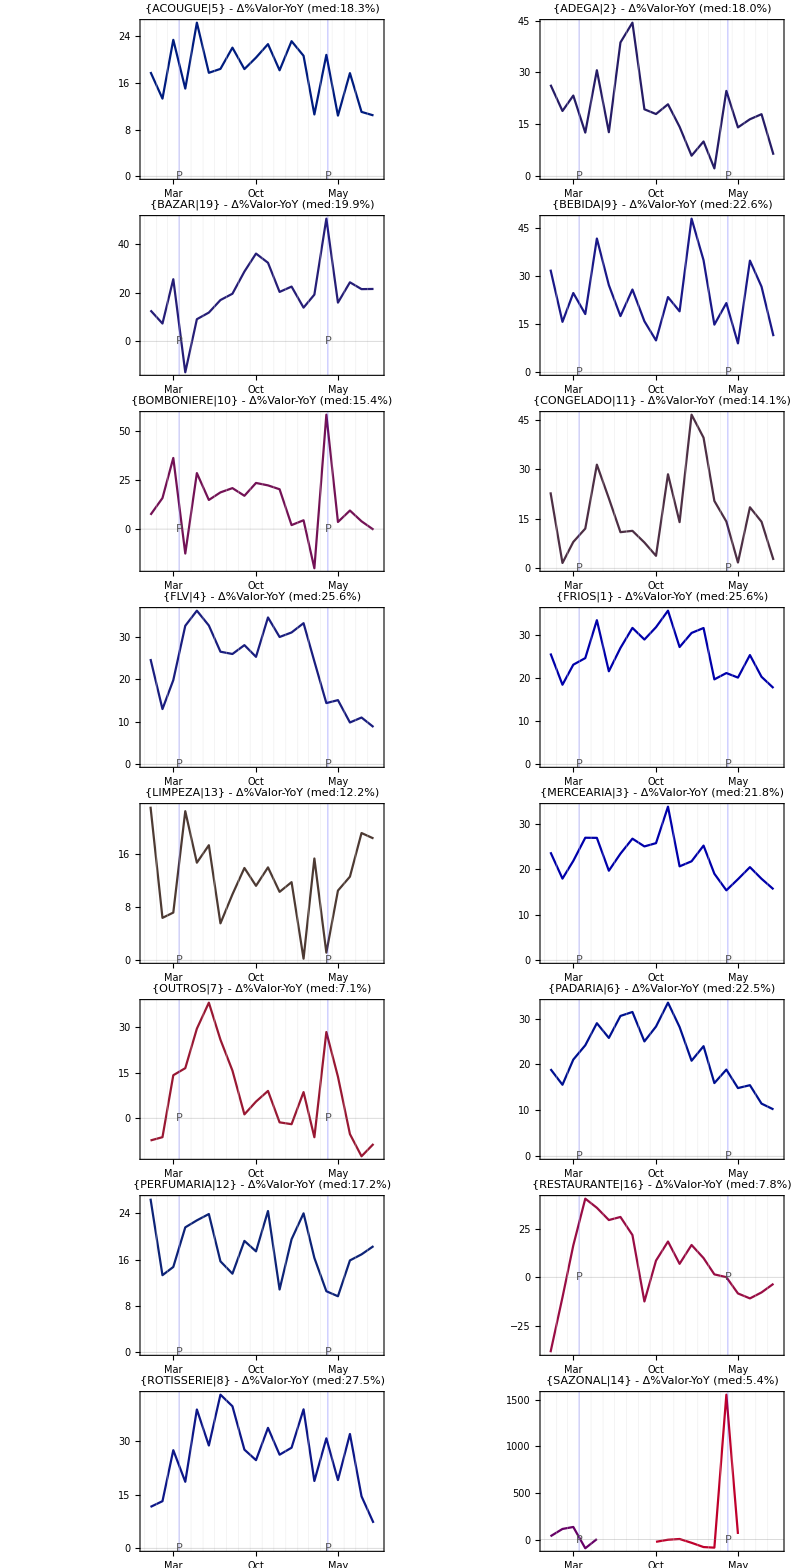
Visão Crescimento Valor

YoY por Dep Lojas +14 meses

-Graphics-

```mathematica
ClearAll@reportDep;
reportDep[field:("Valor"|"Ticket"|"TM")]:=Module[{rMe14,rMa14,plotsMa14,plotsMe14,title},

	plotsMa14=plotLag12Perc[$dataDepMa14[#],field,"StartDate"-> {2013,1,1}]&/@Keys@KeyDrop[$dep, 0];
	plotsMe14=plotLag01Perc[$dataDepMe14[#],field,"StartDate"-> {2013,1,1}]&/@Keys@KeyDrop[$dep, 0];

	rMa14=maReportFrame[
		Style["YoY por Dep Lojas +14 meses\n",$titleStyle]
		,Grid[Partition[plotsMa14,2,2,1,Null],Spacings->0]
	];

	(*
	rMe14=maReportFrame[
		Style["MoM por Dep Lojas -14 meses\n",$titleStyle]
		,Grid[Partition[plotsMe14,2,2,1,Null],Spacings->0]
	];*)

	title=Style["\nVisão Crescimento "<>field<>"\n",15,$titleStyle];
	maReportFrame[title,Grid[{{rMa14}(*,{},{rMe14}*)}]]

]

rep[1]=reportDep["Valor"]
(*rep[2]=reportDep["Ticket"]*)
(*rep[3]=reportDep["TM"]*)
```

### Departamento 2

```mathematica
ClearAll@reportDep2;
reportDep2[field:("Valor"|"Ticket"|"TM")]:=Module[{r2Me14,r2Ma14,rGeral,plots2Ma14,plots2Me14,plotsGeral,title},

	plots2Ma14=plotLag12Perc[$dataDep2Ma14[#],field,"StartDate"-> {2013,1,1}]&/@Keys@KeyDrop[$dep, 0];
	plots2Me14=plotLag01Perc[$dataDep2Me14[#],field,"StartDate"-> {2013,1,1}]&/@Keys@KeyDrop[$dep, 0];
	plotsGeral=plotLag12Perc[$dataDep2[0],field,"StartDate"-> {2013,1,1}]

	r2Ma14=maReportFrame[
		Style["YoY por Dep Lojas +14 meses\n",$titleStyle]
		,Grid[Partition[plots2Ma14,2,2,1,Null],Spacings->0]
	];
	
	rGeral=maReportFrame[
		Style["Grupo\n",$titleStyle],plotsGeral
	];	
	
	r2Me14=maReportFrame[
		Style["YoY por Dep Lojas +14 meses\n",$titleStyle]
		,Grid[Partition[plots2Me14,2,2,1,Null],Spacings->0]
	];

	title=Style["\nVisão Crescimento "<>field<>"\n",15,$titleStyle];

	maReportFrame[title
				,Grid[{
					{rGeral}
				 (*,{rGrupoMa14,rGrupoMe14}*)
				   ,{r2Ma14}
				   ,{r2Me14}
				}]]

]

rep[1]=reportDep2["Valor"]
(*rep[2]=reportDep["Ticket"]*)
(*rep[3]=reportDep["TM"]*)
```

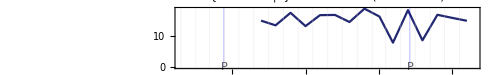
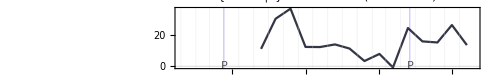
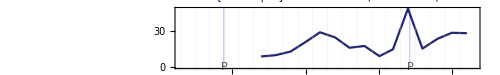
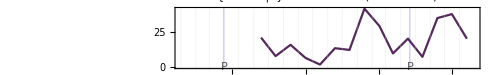
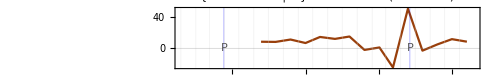
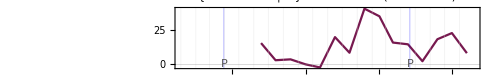
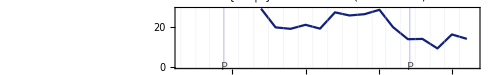
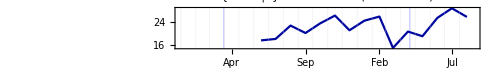
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotLag12Perc[$dataDep2Ma14[#],"Valor","StartDate"-> {2013,1,1}]&/@Keys@KeyDrop[$dep, 0]
```

```mathematica
.
```

```mathematica
Scan[Export[#<>".png",reportLoja[#],ImageResolution-> 150]&,{"Valor","Ticket","TM"}]
```

```mathematica
$InstallationDirectory/SystemFiles/FrontEnd/TextResources/Macintosh/KeyEventTranslations.tr
```

(C:\Program Files\Wolfram Research\Mathematica\10.0)/(FrontEnd Macintosh SystemFiles TextResources KeyEventTranslations.tr)

## Test

```mathematica
plotReport[r,"Valor"]
plotReport[r,"Ticket"]
plotReport[r,"TM"]
```

```mathematica
(*$dataLoja=AssociationMap[(PrintTemporary@#;getVendaLoja[#,{{2012,1,1},{2014,8,31}}])&,(*Query[;;3]@*)Keys@$lojas];*)
reportLoja["Valor"]
reportLoja["Ticket"]
reportLoja["TM"]
```

## Notas

Forma inteligente de agrupar entre meses OK!
Compactar vizualizacao PlotLogPerc OK

Fazer para departamentos (primeiro agrupado, depois por loja)